## 1.

```mathematica
x = {3,15,16,16,19,20,20,21,22,22,25,25,25,25,30,33,33,35,35,35,35,36,40,45,46,52,70}
```

{3,15,16,16,19,20,20,21,22,22,25,25,25,25,30,33,33,35,35,35,35,36,40,45,46,52,70}

```mathematica
y=Partition[x, 3]
```

{{3,15,16},{16,19,20},{20,21,22},{22,25,25},{25,25,30},{33,33,35},{35,35,35},{36,40,45},{46,52,70}}

```mathematica
z=Map[Mean, y]//N
```

{11.3333,18.3333,21.,24.,26.6667,33.6667,35.,40.3333,56.}

```mathematica
f1 := Transpose[{Range[Length[x]], x}]
f2 = Transpose[{Range[Length[z]]*3, z}]
```

{{3,11.3333},{6,18.3333},{9,21.},{12,24.},{15,26.6667},{18,33.6667},{21,35.},{24,40.3333},{27,56.}}

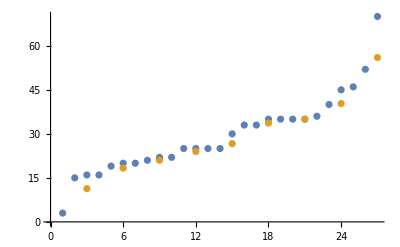

```mathematica
ListPlot[{f1, f2}]
```

This method of binning does a great job at maintaining the curve with considerably less points.

```mathematica
Quantile[x, {.2,.4,.6,.8,1}]
```

{20,25,33,36,70}

```mathematica
InterquartileRange[x]//N
```

```mathematica
l=14.75
```

14.75

```mathematica
Outlier = 1.5 * l
```

22.125

```mathematica
36 + Outlier
```

58.125

```mathematica
25-Outlier
```

2.875

It seems that 70 is an outlier.

```mathematica
minmax=(35-13)/(70-13)*(1-0) + 0//N
```

0.385965

```mathematica
zscore=(35 - Mean[x])/StandardDeviation[x]//N
```

0.398368

```mathematica
decimal=35/100//N
```

0.35